```mathematica
(*Mathenatica*)
```

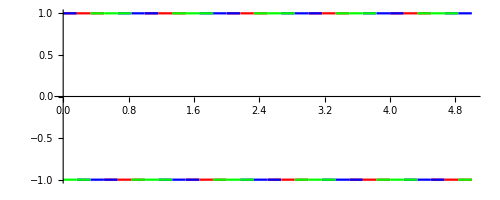

```mathematica
Plot[{SquareWave[x],SquareWave[x+1/3],SquareWave[x-1/3]},{x,0,5},PlotStyle->{Red,Blue,Green},AspectRatio->Automatic]
```

```mathematica
Clear[s0,s,c,k,x]
```

```mathematica
s0=N[Log[2]/Log[3]]
```

0.63093

```mathematica
(* triaxial 1/3 phase Triangle wave fractal function :ratio 2 :s=Log[2]/Log[3]*)
```

```mathematica
c1[x_]=Sum[SquareWave[2^k*(x)]/(2^(s0*k)),{k,0,20}];
```

```mathematica
c2[x_]=Sum[SquareWave[2^k*(x+1/3)]/(2^(s0*k)),{k,0,20}];Sum[TriangleWave[3^k*(x+0.25)]/(3^(s0*k)),{k,0,20}];
```

```mathematica
c3[x_]=Sum[SquareWave[2^k*(x-1/3)]/(2^(s0*k)),{k,0,20}];Sum[TriangleWave[3^k*(x+0.25)]/(3^(s0*k)),{k,0,20}];
```

```mathematica
g0=ParametricPlot3D[{c1[x],c2[x],c3[x]},{x,0,1},ColorFunction->Hue,AspectRatio->1,ImageSize->{2000,2000},PlotPoints->200];
Export["SquareWave_triaxial3d_ratio2_Fractal200.jpg",g0]
```

SquareWave_triaxial3d_ratio2_Fractal200.jpg

```mathematica
(* triaxial 3D cylinder Triangle wave fractal function *)
```

```mathematica
w=Flatten[ParallelTable[N[{c1[x]*c1[y],c2[x]*c2[y],c3[x]*c3[y]}],{x,0,1,1/600},{y,0,1,1/600}],1];
```

```mathematica
Length[w]
```

361201

```mathematica
g1=ListPointPlot3D[w,ColorFunction->"CMYKColors", ImageSize->{2000,2000}];
```

```mathematica
g2=Show[g1,ViewPoint->Bottom,ImageSize->{2000,2000}];
```

```mathematica
g3=Show[g1,ViewPoint->Front,ImageSize->{2000,2000}];
```

```mathematica
g4=Show[g1,ViewPoint->{2,2,-2},ImageSize->{2000,2000}];
```

```mathematica
Export["SquareWave_Triaxial4_3d_fractal_360000_ratio2_grid.jpg",Rasterize[GraphicsGrid[{{g1,g2},{g3,g4}}],"Image",ImageSize->4000]]
```

SquareWave_Triaxial4_3d_fractal_360000_ratio2_grid.jpg

```mathematica
Clear[g1,g2,g3,g4]
```

```mathematica
pts=Union[w];
(* Voxelization: 3d voxel projection on Cuboids*)
voxel=0.015
```

0.015

```mathematica
Dimensions[pts]
```

{180300,3}

```mathematica
voxels=DeleteDuplicates[Floor[pts/voxel]];
cuboids={Hue[Abs[1-Norm[#]/30]],Cuboid[#*voxel,(#+1)*voxel]}&/@voxels;

(*7. Render voxel fractal*)
g1=Graphics3D[{Pink,EdgeForm[],cuboids},Boxed->False,Background->Black,ImageSize->{2000,2000}];
Export["SquareWave_Triaxial4_3d_fractal_360000_ratio2_voxel_BackBlack_g1.jpg",g1];
```

```mathematica
g2=Show[g1,ViewPoint->Above,ImageSize->{2000,2000}];
Export["SquareWave_Triaxial4_3d_fractal_360000_ratio2_voxel_BackBlack_g2.jpg",g2];
```

```mathematica
g3=Show[g1,ViewPoint->Front,ImageSize->{2000,2000}];
Export["SquareWave_Triaxial4_3d_fractal_360000_ratio2_voxel_BackBlack_g3.jpg",g3];
```

```mathematica
g4=Show[g1,ViewPoint->{2.,2,-2},ImageSize->{2000,2000}];
Export["SquareWave_Triaxial4_3d_fractal_360000_ratio2_voxel_BackBlack_g4.jpg",g4];
```

```mathematica
Export["SquareWave_Triaxial4_3d_fractal_360000_ratio2_voxel_BackBlack_grid.jpg",Rasterize[GraphicsGrid[{{g1,g2},{g3,g4}}],"Image",ImageSize->4000]];
```

```mathematica
(*export 3d model and Clean the model for printing*)
```

```mathematica
Export["SquareWave_Triaxial4_3d_fractal_360000_ratio2_voxel_BackBlack.stl",g1]
```

```mathematica
model =Import["SquareWave_Triaxial4_3d_fractal_360000_ratio2_voxel_BackBlack.stl"]
```

```mathematica
prt=Printout3D[model,"SquareWave_Triaxial3_3d_fractal_360000_ratio3_voxel_BackBlack_stl_PRT.stl"]
(*end*)
```